```mathematica
SetDirectory[NotebookDirectory[]];
Directory[]
Off[Needs::nocont];Needs["LowDiscrep`"];
On[Needs::nocont];
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma

## Geometry

We consider a 1D geometry [0,1] and consider all pairs within δ of one another.

```mathematica
(* Distance function between two pairs *)
```

```mathematica
Clear[distFunc];
distFunc[{x_}, {y_}, δ_:0.2]:= If[Abs[x-y] < δ, 1.0, 0.0];
```

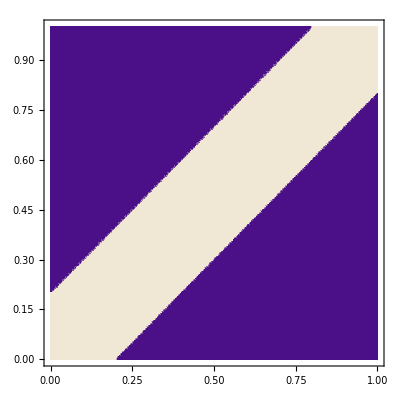

```mathematica
(* Plot this function *)
DensityPlot[distFunc[{x}, {y}], {x, 0,1}, {y, 0, 1}, PlotPoints->100]
```

```mathematica
(* Define analytic RR *)
analyticRR[δ_:0.2] := NIntegrate[distFunc[{x},{y}, δ], {x,0,1}, {y, 0, 1}];
```

```mathematica
analyticRR[]
```

0.36

## Random vs LDS grids

```mathematica
Clear[flatten1d];
flatten1d[x_]:= Flatten[x,{{1},{2,3}}];
```

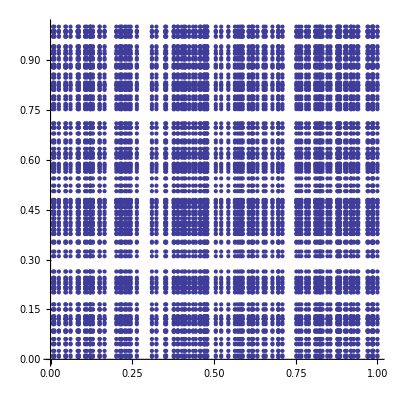

```mathematica
ListPlot[flatten1d[generateRandomGrid[100]], AspectRatio->1]
```

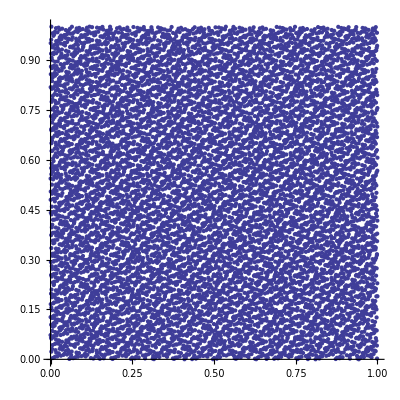

```mathematica
ListPlot[flatten1d[generateLDSshiftedGrid[100^2]], AspectRatio->1]
```

## Simple Monte Carlo Integration

Start by comparing errors for 100^2points.

```mathematica
v1 = Reap[Do[Sow[mcIntegrate[distFunc, generateRandomGrid[100, 1]]],{500}]][[2,1]];
```

```mathematica
v2 = Reap[Do[Sow[mcIntegrate[distFunc, generateLDSshiftedGrid[100^2,2]]], {500}]][[2,1]];
```

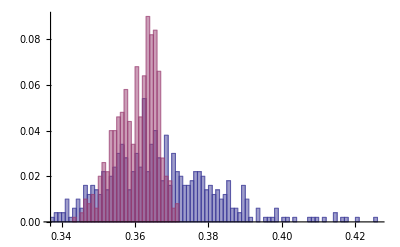

```mathematica
Histogram[{v1, v2}, {0.001}, "Probability"]
```

```mathematica
rootnvals = {10,40, 160, 640};
nvals = rootnvals^2;
```

```mathematica
ran1 = Table[getmeanerror[mcIntegrate[distFunc, generateRandomGrid[ii,1]], 100], {ii, rootnvals}];
```

```mathematica
ran1/analyticRR[]
```

{{1.13222,0.179158},{1.05726,0.0740354},{1.00898,0.027647},{1.00516,0.0145135}}

```mathematica
lds1 = Table[getmeanerror[mcIntegrate[distFunc, generateLDSshiftedGrid[ii,2]], 100], {ii, nvals}];
```

```mathematica
lds1/analyticRR[]
```

{{0.993611,0.143436},{1.00309,0.0306167},{0.99902,0.0131237},{0.999978,0.000831146}}

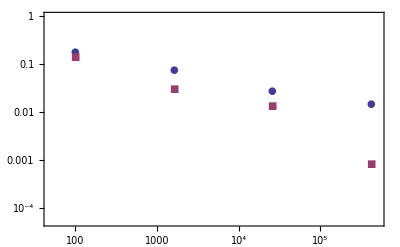

```mathematica
ListLogLogPlot[{Transpose[{nvals, ran1[[All,2]]/analyticRR[]}], Transpose[{nvals, lds1[[All, 2]]/analyticRR[]}]}, Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{{50, 500000}, {5.*^-5, 1}}]
```